```mathematica
Quit[]
```

```mathematica
up:={{1,0}}
```

```mathematica
dn:={{0,1}}
```

```mathematica
nn=4;λ=0.1;g1=0.1;
```

```mathematica
term[k_,j_]:=If[k==j||k==j+1&& j!=nn, PauliMatrix[3],IdentityMatrix[2]];
term[k_,nn]:=If[k==1||k==nn, PauliMatrix[3],IdentityMatrix[2]];ttZZ[j_]:=KroneckerProduct@@Table[term[kk,j],{kk,1,nn}];
term2[k_,j_]:=If[k==j, PauliMatrix[1],IdentityMatrix[2]];
term3[k_,j_]:=If[k==j, PauliMatrix[3],IdentityMatrix[2]];
ttX[j_]:=KroneckerProduct@@Table[term2[kk,j],{kk,1,nn}];
ttZ[j_]:=KroneckerProduct@@Table[term3[kk,j],{kk,1,nn}];
H=-J Sum[ttZZ[j],{j,1,nn}]-hx Sum[ttX[j],{j,1,nn}]-hz Sum[ttZ[j],{j,1,nn}];
HH=H/J/.{hx->g1 J, hz->g2 J}/.g2->λ g1//Simplify;
```

```mathematica
ψ0:=Transpose[KroneckerProduct[up,dn,up,dn]//Flatten]
```

```mathematica
ψ[t_]:=MatrixExp[-I t HH].ψ0
```

```mathematica
mz[t_,j_]:=Conjugate[Transpose[ψ[t]]].ttZ[j].ψ[t]
```

```mathematica
mx[t_,j_]:=Conjugate[Transpose[ψ[t]]].ttX[j].ψ[t]
```

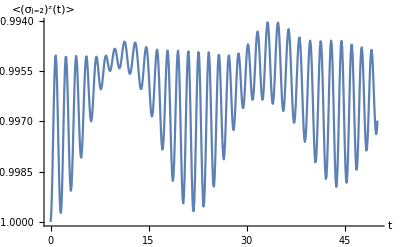

```mathematica
ListPlot[Table[{t,mz[t,2]},{t,0,50,.1}],Joined->True,AxesLabel->{"t","<(σ_(j=2))^z(t)>"}]
```

```mathematica
Export["mzvst.png",%44]
```

mzvst.png

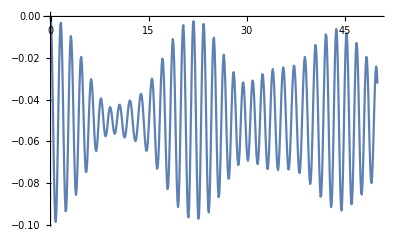

```mathematica
ListPlot[Table[{t,mx[t,2]},{t,0,50,.1}],Joined->True]
```

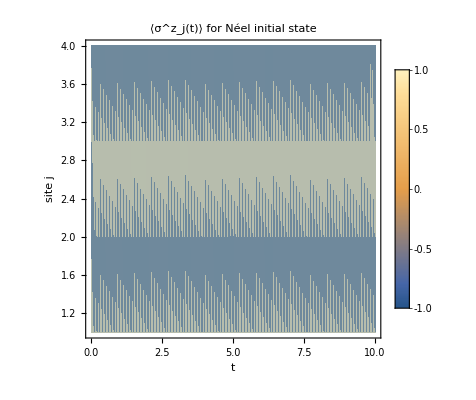

```mathematica
(*say you've set psi[t_] and expectation[t_,j_] already,with integer j*)tmax=10;
dt=0.1;

data={};Do[AppendTo[data,{t,j,Re[mz[t,j]]}],{j,1,4},(*sites*){t,0,tmax,dt}           (*times*)];

ListDensityPlot[data,(*x=t,y=j*)(*blocky,emphasises discreteness*)FrameLabel->{"t","site j"},PlotLabel->"⟨σ^z_j(t)⟩ for Néel initial state",PlotLegends->Automatic]
```

```mathematica
Export["neel.png",%151]
```

neel.png

```mathematica
ψ0:=Transpose[KroneckerProduct[up,dn,dn,dn]//Flatten]
```

```mathematica
ψ[t_]:=MatrixExp[-I t HH].ψ0
```

```mathematica
mz[t_,j_]:=Conjugate[Transpose[ψ[t]]].ttZ[j].ψ[t]
```

```mathematica
mx[t_,j_]:=Conjugate[Transpose[ψ[t]]].ttX[j].ψ[t]
```

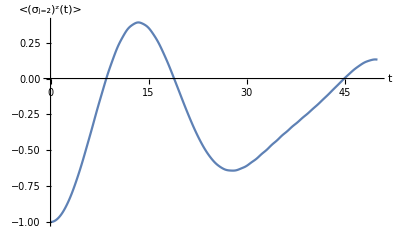

```mathematica
ListPlot[Table[{t,mz[t,2]},{t,0,50,.1}],Joined->True,AxesLabel->{"t","<(σ_(j=2))^z(t)>"}]
```

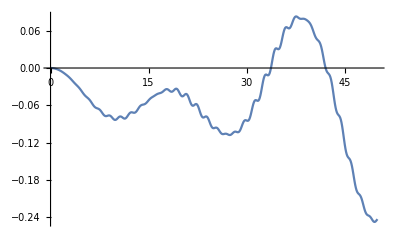

```mathematica
ListPlot[Table[{t,mx[t,2]},{t,0,50,.1}],Joined->True]
```

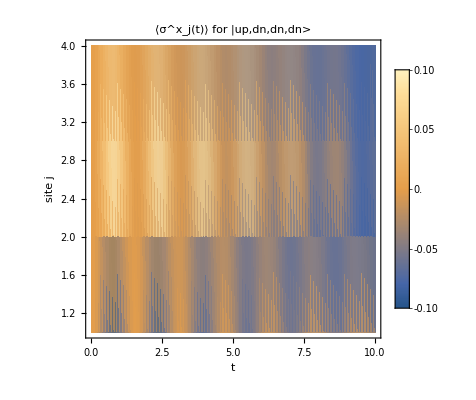

```mathematica
(*say you've set psi[t_] and expectation[t_,j_] already,with integer j*)tmax=10;
dt=0.1;

data={};Do[AppendTo[data,{t,j,Re[mx[t,j]]}],{j,1,4},(*sites*){t,0,tmax,dt}           (*times*)];

ListDensityPlot[data,(*x=t,y=j*)(*blocky,emphasises discreteness*)FrameLabel->{"t","site j"},PlotLabel->"⟨σ^x_j(t)⟩ for |up,dn,dn,dn>",PlotLegends->Automatic]
```

```mathematica
ψ0:=Transpose[KroneckerProduct[up,dn,dn,up]//Flatten]
```

```mathematica
ψ[t_]:=MatrixExp[-I t HH].ψ0
```

```mathematica
mz[t_,j_]:=Conjugate[Transpose[ψ[t]]].ttZ[j].ψ[t]
```

```mathematica
mx[t_,j_]:=Conjugate[Transpose[ψ[t]]].ttX[j].ψ[t]
```

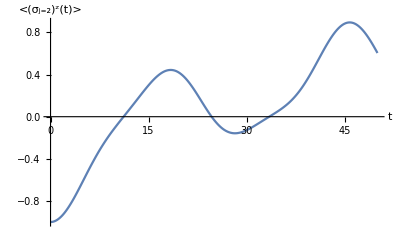

```mathematica
ListPlot[Table[{t,mz[t,2]},{t,0,50,.1}],Joined->True,AxesLabel->{"t","<(σ_(j=2))^z(t)>"}]
```

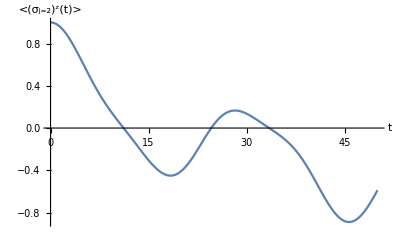

```mathematica
ListPlot[Table[{t,mz[t,4]},{t,0,50,.1}],Joined->True,AxesLabel->{"t","<(σ_(j=2))^z(t)>"}]
```

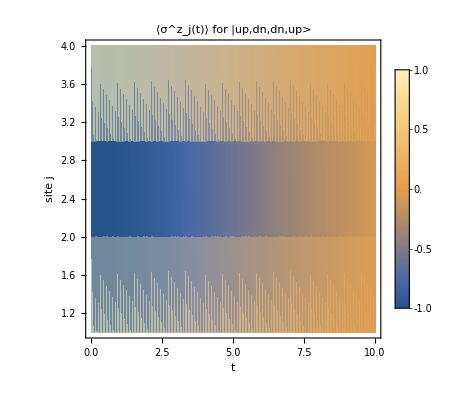

```mathematica
(*say you've set psi[t_] and expectation[t_,j_] already,with integer j*)tmax=10;
dt=0.1;

data={};Do[AppendTo[data,{t,j,Re[mz[t,j]]}],{j,1,4},(*sites*){t,0,tmax,dt}           (*times*)];

ListDensityPlot[data,(*x=t,y=j*)(*blocky,emphasises discreteness*)FrameLabel->{"t","site j"},PlotLabel->"⟨σ^z_j(t)⟩ for |up,dn,dn,up>",PlotLegends->Automatic]
```

```mathematica
Export["scatising.png",%190]
```

scatising.png